```mathematica
VMagTot1;
VMagTot2;
VMagTot4;
VMagTot8;
```

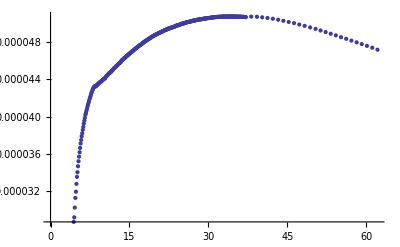

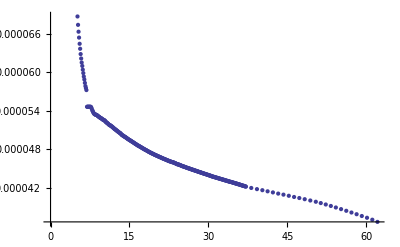

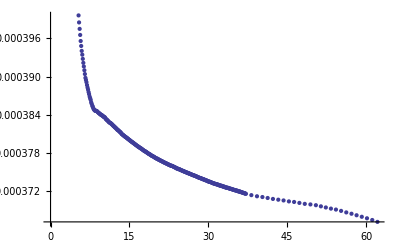

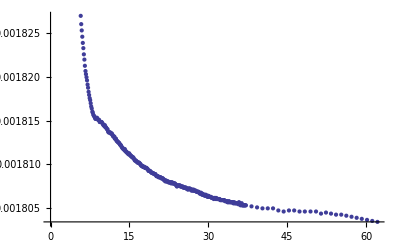

```mathematica
ListPlot[{Transpose[{T1Tot,VMagTot1}]}]
ListPlot[{Transpose[{T2Tot,VMagTot2}]}]
ListPlot[{Transpose[{T4Tot,VMagTot4}]}]
ListPlot[{Transpose[{T8Tot,VMagTot8}]}]
```

```mathematica
FullCurr1;
FullCurr2;
FullCurr4;
FullCurr8;
```

```mathematica
θRadFull1 = θ1Full*Pi/180;
θRadFull2 = θ2Full*Pi/180;
θRadFull4 = θ4Full*Pi/180;
θRadFull8 = θ8Full*Pi/180;
```

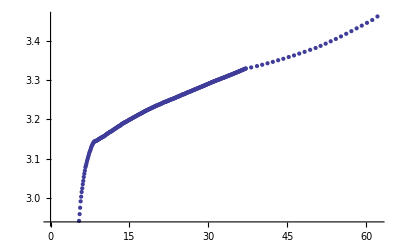

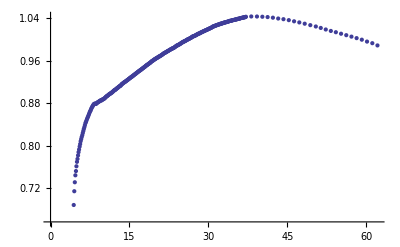

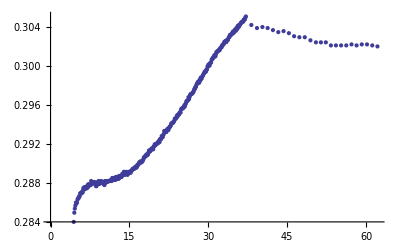

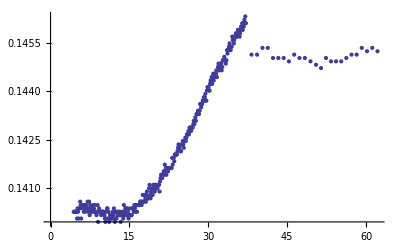

```mathematica
ListPlot[{Transpose[{T1Tot,θRadFull1}]}]
ListPlot[{Transpose[{T2Tot,θRadFull2}]}]
ListPlot[{Transpose[{T4Tot,θRadFull4}]}]
ListPlot[{Transpose[{T8Tot,θRadFull8}]}]
```

```mathematica
VMagCorr1 = VMagTot1 / FullCurr1;
VMagCorr2 = VMagTot2 / FullCurr2
VMagCorr4 = VMagTot4 / FullCurr4;
VMagCorr8 = VMagTot8 / FullCurr8;
```

{0.789971,0.790837,0.792063,0.792795,0.788706,0.766359,0.673421,0.566315,0.456424,0.422,0.410569,0.38885,0.371174,0.345346,0.309404,0.274462,0.22266,0.215507,0.211558,0.207898,0.19985,0.194794,0.189529,0.111289,0.101241,0.0955611,0.0915234,0.0893413,0.0868504,0.0847758,0.0834922,0.0819059,0.0806075,0.0794927,0.0783228,0.0773788,0.0763714,0.0755383,0.0747734,0.0741321,0.0734258,0.0727819,0.0721311,0.0715703,0.0709247,0.0703209,0.0699538,0.0695681,0.0664098,0.0664099,0.0664106,0.0664106,0.0664102,0.0664111,0.0664102,0.06641,0.0663026,0.0660629,0.0657565,0.0655778,0.0653407,0.0651474,0.0650428,0.0649845,0.0649146,0.0649359,0.0648653,0.0648347,0.0647203,0.064629,0.0645544,0.0645354,0.0644303,0.0643266,0.0643064,0.0642146,0.0642046,0.0640497,0.0640492,0.0639358,0.0638796,0.0638568,0.0638219,0.0636641,0.0635221,0.0634895,0.0633712,0.0633188,0.0632381,0.0631337,0.0630364,0.062962,0.0629249,0.0628925,0.062782,0.0627332,0.0626466,0.062549,0.0624818,0.062366,0.0622976,0.062202,0.0621548,0.0620763,0.0619743,0.061929,0.0618212,0.0617645,0.0616943,0.0616074,0.061528,0.0614656,0.0614263,0.0612662,0.0611649,0.0610931,0.0610407,0.0609825,0.0608929,0.0608417,0.0607925,0.0607357,0.0606535,0.0606066,0.0605099,0.060442,0.0603916,0.0603158,0.0602478,0.0601888,0.0601282,0.0600875,0.0600132,0.059949,0.0598855,0.0598311,0.0597646,0.0597011,0.0596261,0.0595773,0.0594962,0.0594526,0.0593947,0.0593089,0.0592396,0.0591947,0.0591606,0.0590864,0.0590485,0.0589843,0.05893,0.058864,0.0588293,0.0587552,0.0587001,0.058653,0.0585934,0.0585272,0.0584857,0.0584319,0.0583952,0.0583303,0.058278,0.0582231,0.0581623,0.058122,0.058067,0.0580133,0.0579709,0.0579064,0.0578709,0.0578133,0.057785,0.0577435,0.0576914,0.0576359,0.0575964,0.0575496,0.0575024,0.0574715,0.0574191,0.0573854,0.0573445,0.057306,0.0572498,0.0572042,0.0571818,0.0571482,0.0570972,0.0570432,0.0570085,0.0569632,0.0569312,0.0568876,0.0568458,0.0568079,0.0567889,0.0567287,0.0566999,0.0566555,0.0566207,0.0565814,0.0565387,0.0565189,0.056466,0.0564314,0.0564096,0.0563703,0.0563422,0.0563015,0.0562929,0.0562716,0.0562345,0.0562111,0.0561749,0.0561281,0.0560931,0.0560556,0.0559772,0.0559418,0.0559313,0.0559035,0.0558676,0.0558451,0.0558142,0.0557741,0.05574,0.0556912,0.0556518,0.0556091,0.0555833,0.0555563,0.0555351,0.0554952,0.0554665,0.0554395,0.0553991,0.055361,0.0553146,0.0553095,0.0552819,0.0552361,0.0552207,0.0551906,0.0551643,0.0551293,0.0550999,0.0550727,0.0550134,0.0550084,0.0549977,0.0549475,0.0549193,0.054894,0.0548616,0.0548339,0.0548085,0.0547788,0.0547438,0.0547263,0.0546825,0.0546522,0.0546268,0.0545998,0.0545731,0.0545565,0.054512,0.0544855,0.0544561,0.0544299,0.0543942,0.0543744,0.0543484,0.0543165,0.0542961,0.0542709,0.0542308,0.054202,0.0541807,0.054151,0.0541247,0.0540993,0.0540721,0.0540468,0.0540071,0.0539812,0.0539302,0.0539127,0.0538948,0.0538765,0.0538389,0.0538238,0.0537929,0.0537645,0.0537416,0.0537172,0.0536976,0.0536657,0.053639,0.0536171,0.0535935,0.0535588,0.053547,0.0535175,0.0534885,0.053469,0.05344,0.0534244,0.0534044,0.0533628,0.0533437,0.053322,0.0532996,0.0532707,0.0532417,0.0532276,0.0531917,0.0531692,0.0531551,0.0531215,0.0530953,0.053076,0.0530726,0.0530386,0.053016,0.0529829,0.0529635,0.0529371,0.0529127,0.0528849,0.0528583,0.0528335,0.0528141,0.0527944,0.0527636,0.0527436,0.0527233,0.052696,0.0526654,0.0526379,0.0526135,0.0525895,0.0525679,0.0525329,0.052496,0.0524823,0.0524707,0.0524393,0.0524128,0.0523863,0.0523545,0.0521233,0.051927,0.0517543,0.0515742,0.0514036,0.0512154,0.0510579,0.050883,0.0506995,0.0505476,0.0503686,0.050174,0.049988,0.0497949,0.0495847,0.0493693,0.049144,0.0489033,0.0486583,0.0484051,0.0481555,0.0478906,0.0476333,0.0473474,0.0470168}

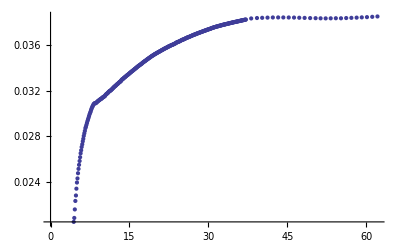

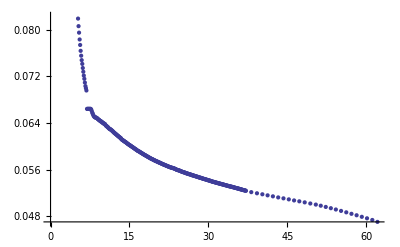

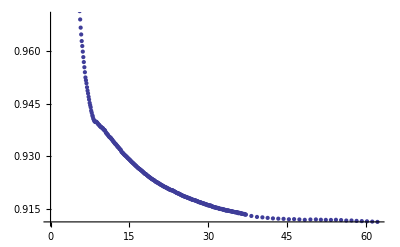

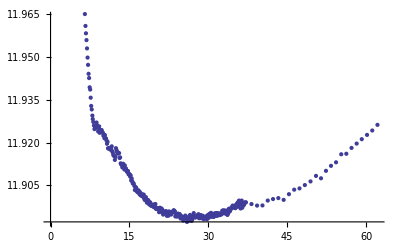

```mathematica
ListPlot[{Transpose[{T1Tot,VMagCorr1}]}]
ListPlot[{Transpose[{T2Tot,VMagCorr2}]}]
ListPlot[{Transpose[{T4Tot,VMagCorr4}]}]
ListPlot[{Transpose[{T8Tot,VMagCorr8}]}]
```

```mathematica
T1Tot
T2Tot
T4Tot
T8Tot
```

{4.40631,4.51054,4.61289,4.71498,4.82758,4.91473,5.01815,5.11954,5.22004,5.31913,5.41668,5.52622,5.62089,5.71625,5.81773,5.91434,6.02604,6.12616,6.22141,6.31404,6.41872,6.52122,6.62392,6.72095,6.8185,6.92624,7.02741,7.12272,7.2247,7.31531,7.4233,7.52693,7.62608,7.71345,7.81597,7.92686,8.01586,8.1172,8.23302,8.32545,8.43155,8.51337,8.62378,8.7176,8.82903,8.92762,9.02352,9.12809,9.22233,9.31926,9.42457,9.52371,9.62356,9.72367,9.82929,9.93562,10.035,10.1294,10.2284,10.3222,10.4212,10.5216,10.6275,10.7261,10.8305,10.9228,11.0163,11.1294,11.2219,11.3224,11.4211,11.5261,11.624,11.7284,11.8215,11.9241,12.0253,12.1221,12.219,12.3293,12.4247,12.5241,12.6247,12.7168,12.8302,12.9139,13.0294,13.1197,13.2252,13.3303,13.4232,13.5209,13.6281,13.7298,13.8248,13.9267,14.027,14.1185,14.219,14.3237,14.4211,14.5279,14.6167,14.7245,14.8263,14.9267,15.0326,15.1201,15.2207,15.326,15.4236,15.5235,15.6277,15.721,15.825,15.9288,16.027,16.1267,16.2212,16.3219,16.4171,16.5232,16.6249,16.7214,16.8251,16.9254,17.0261,17.1254,17.2278,17.3245,17.4228,17.5188,17.6225,17.7268,17.8237,17.9224,18.0177,18.12,18.2285,18.3169,18.4208,18.5233,18.622,18.721,18.8193,18.9273,19.0207,19.1189,19.2227,19.3176,19.4246,19.5213,19.6264,19.7311,19.8168,19.9166,20.0192,20.1265,20.2146,20.3197,20.4193,20.5192,20.6278,20.7202,20.818,20.9258,21.0233,21.127,21.2237,21.3221,21.4195,21.5239,21.6181,21.7255,21.8185,21.9271,22.0229,22.1199,22.2173,22.3241,22.4169,22.5215,22.6204,22.7269,22.8208,22.922,23.0235,23.1199,23.2255,23.3139,23.4191,23.5201,23.6239,23.727,23.8227,23.9222,24.02,24.1184,24.2257,24.3163,24.4158,24.5203,24.6198,24.7276,24.82,24.9249,25.0234,25.1302,25.2259,25.3251,25.4259,25.5242,25.6209,25.7267,25.8223,25.9265,26.0294,26.1333,26.2185,26.3249,26.4222,26.5215,26.6222,26.725,26.8289,26.92,27.0209,27.1216,27.2173,27.3253,27.422,27.5174,27.6285,27.7333,27.8192,27.9324,28.0292,28.1142,28.2359,28.3338,28.4212,28.5333,28.6144,28.7216,28.8229,28.9283,29.0288,29.1143,29.2282,29.3257,29.4254,29.5123,29.6181,29.7207,29.8185,29.9292,30.0331,30.1159,30.2237,30.318,30.4092,30.514,30.6208,30.7117,30.8135,30.9466,31.0074,31.1201,31.2128,31.3192,31.4203,31.5204,31.6303,31.7188,31.8329,31.9382,32.0365,32.107,32.2408,32.3315,32.4345,32.5173,32.6305,32.7172,32.8401,32.9399,33.0192,33.1315,33.2052,33.3164,33.4135,33.5291,33.6147,33.7274,33.8378,33.916,34.03,34.1061,34.2193,34.3143,34.4396,34.5252,34.6199,34.7145,34.8254,34.9337,35.0204,35.133,35.2295,35.3213,35.4239,35.5227,35.6272,35.7148,35.8155,35.9289,36.0285,36.1174,36.2158,36.3322,36.4168,36.5328,36.6182,36.742,36.8282,36.938,37.0253,37.1194,38.1278,39.2309,40.2174,41.2317,42.2419,43.2529,44.2359,45.2607,46.2699,47.2625,48.2793,49.3329,50.3654,51.3167,52.2798,53.2406,54.214,55.192,56.1832,57.1674,58.1656,59.1416,60.1293,61.1343,62.1239}

{2.09,2.12,2.15,2.18,2.21,2.23,2.25,2.31,2.35,2.4,2.46,2.485,2.5,2.53,2.6,2.7,2.98,3.03,3.064,3.1,3.165,3.2,3.25,4.40769,4.51374,4.61423,4.71822,4.83188,4.91909,5.02489,5.12419,5.22749,5.32432,5.42071,5.53274,5.62758,5.72191,5.82314,5.91976,6.03136,6.1298,6.22713,6.32105,6.42523,6.52618,6.63174,6.72666,6.82057,6.93276,7.03163,7.12773,7.232,7.31936,7.43178,7.53195,7.6309,7.7209,7.82272,7.93771,8.01965,8.11854,8.24088,8.33587,8.44081,8.518,8.63295,8.7272,8.83307,8.9332,9.02954,9.13712,9.2234,9.32898,9.43086,9.52399,9.62994,9.72669,9.84081,9.94339,10.044,10.1375,10.2321,10.3261,10.4272,10.5321,10.6325,10.7334,10.8349,10.9252,11.0188,11.1356,11.2317,11.3267,11.4213,11.5326,11.6306,11.734,11.8274,11.9281,12.0304,12.1312,12.2256,12.3348,12.4281,12.5364,12.6341,12.7243,12.8336,12.9197,13.0344,13.1207,13.2268,13.3311,13.4293,13.5222,13.634,13.7363,13.8254,13.936,14.0352,14.1198,14.2228,14.33,14.4245,14.5368,14.6218,14.7244,14.8272,14.93,15.0368,15.1244,15.2227,15.329,15.4278,15.5272,15.6316,15.7219,15.8237,15.9346,16.0317,16.1316,16.2214,16.3227,16.4254,16.5309,16.6307,16.7249,16.834,16.9293,17.033,17.1274,17.234,17.3255,17.4323,17.5219,17.6269,17.7295,17.8289,17.9275,18.0189,18.1237,18.2361,18.3224,18.4275,18.53,18.6214,18.7269,18.8245,18.9301,19.027,19.1197,19.2331,19.3157,19.4224,19.5228,19.6321,19.7349,19.818,19.9228,20.0248,20.133,20.2165,20.3261,20.4254,20.5262,20.6306,20.7237,20.8152,20.9275,21.0254,21.1339,21.2281,21.3249,21.4239,21.5277,21.6191,21.7276,21.8233,21.9312,22.0316,22.1237,22.2247,22.3342,22.4186,22.5271,22.625,22.7282,22.8274,22.9299,23.0281,23.1194,23.2286,23.3115,23.4235,23.5196,23.629,23.7286,23.8281,23.9248,24.0242,24.1214,24.2274,24.3183,24.4207,24.5257,24.6227,24.7326,24.8237,24.9281,25.0308,25.1356,25.2249,25.3273,25.4273,25.5305,25.6252,25.7283,25.8308,25.9296,26.0321,26.1328,26.2201,26.3183,26.426,26.5236,26.6293,26.73,26.8266,26.9245,27.0255,27.1295,27.2186,27.3324,27.4367,27.5266,27.632,27.7363,27.83,27.9262,28.0397,28.1163,28.2395,28.341,28.4362,28.5309,28.6315,28.7192,28.8292,28.9409,29.0255,29.1288,29.2334,29.3234,29.4331,29.5303,29.6326,29.7358,29.8321,29.9472,30.0236,30.124,30.2342,30.3261,30.4228,30.5276,30.634,30.7161,30.851,30.9267,31.0232,31.1348,31.2318,31.3434,31.4305,31.5281,31.6422,31.7258,31.8434,31.9238,32.0438,32.1385,32.2477,32.3369,32.4411,32.5376,32.6301,32.7538,32.8448,32.9374,33.0262,33.1485,33.2182,33.3249,33.4302,33.5484,33.6469,33.7214,33.8363,33.9275,34.0349,34.1103,34.2447,34.3408,34.4253,34.5381,34.6414,34.7364,34.8466,34.9359,35.0512,35.1408,35.2522,35.3479,35.4501,35.5342,35.6237,35.7275,35.8367,35.9471,36.0363,36.1308,36.2134,36.347,36.4368,36.5383,36.6472,36.744,36.8392,36.9301,37.0424,37.1389,38.1523,39.2354,40.2619,41.2562,42.2651,43.2725,44.2718,45.2873,46.2907,47.284,48.311,49.3738,50.4222,51.3619,52.3123,53.2772,54.2308,55.22,56.2102,57.1965,58.1751,59.1637,60.1532,61.1598,62.1388}

{4.40934,4.51857,4.61653,4.72156,4.83481,4.92343,5.02868,5.12999,5.23237,5.32802,5.42391,5.53659,5.63476,5.72939,5.82872,5.92643,6.03498,6.13248,6.23299,6.32823,6.43377,6.53049,6.63628,6.7317,6.82791,6.93498,7.03598,7.13268,7.23631,7.32666,7.43883,7.53525,7.63423,7.72398,7.82954,7.94766,8.0218,8.12153,8.24618,8.34598,8.44876,8.52632,8.63746,8.73557,8.83745,8.93662,9.03593,9.1461,9.23325,9.33914,9.43823,9.52722,9.63474,9.72468,9.84817,9.94807,10.05,10.1459,10.2386,10.3286,10.4317,10.5408,10.6376,10.7361,10.8375,10.9258,11.0248,11.1405,11.2409,11.3337,11.4293,11.5374,11.6355,11.7372,11.8306,11.9323,12.0377,12.1359,12.2301,12.3403,12.4323,12.5442,12.6404,12.7332,12.8363,12.9259,13.0365,13.1261,13.2308,13.3318,13.4335,13.527,13.6425,13.7404,13.8248,13.9445,14.0409,14.1245,14.226,14.3365,14.4311,14.5426,14.6313,14.7245,14.8271,14.9367,15.0379,15.1313,15.2278,15.3315,15.4347,15.5341,15.6347,15.7247,15.8228,15.9392,16.033,16.1344,16.2265,16.3225,16.435,16.5383,16.6381,16.7308,16.8381,16.9285,17.0393,17.1297,17.2388,17.3275,17.441,17.5288,17.6313,17.734,17.8335,17.9318,18.0261,18.1299,18.2399,18.3265,18.4351,18.5403,18.6206,18.7323,18.8293,18.9317,19.0301,19.1222,19.2433,19.315,19.4247,19.5248,19.6397,19.7355,19.8239,19.9318,20.0298,20.1379,20.2231,20.3305,20.4334,20.5325,20.6334,20.7287,20.8144,20.9274,21.0279,21.1332,21.2324,21.3279,21.4249,21.5298,21.6223,21.7293,21.828,21.9346,22.0355,22.128,22.2329,22.3415,22.4223,22.5325,22.6279,22.7295,22.8321,22.936,23.027,23.1259,23.2292,23.3163,23.4271,23.5226,23.6321,23.7288,23.8304,23.9274,24.0299,24.1296,24.2323,24.3258,24.4254,24.5321,24.6255,24.7328,24.8273,24.9293,25.0409,25.1426,25.2318,25.3345,25.4316,25.5358,25.6307,25.7339,25.8342,25.9359,26.0403,26.1321,26.229,26.3228,26.4269,26.5329,26.6391,26.7311,26.8284,26.9296,27.0296,27.1385,27.2194,27.3395,27.4362,27.5321,27.645,27.7371,27.8349,27.9346,28.0376,28.1244,28.2425,28.3503,28.4401,28.5396,28.6339,28.7222,28.84,28.9457,29.0336,29.1381,29.2453,29.3273,29.4399,29.5419,29.631,29.74,29.8404,29.9517,30.0284,30.124,30.2464,30.3346,30.4299,30.537,30.6391,30.729,30.8608,30.925,31.032,31.1468,31.2314,31.3532,31.4372,31.5285,31.638,31.7321,31.8494,31.9347,32.0398,32.1486,32.2563,32.3442,32.4418,32.5491,32.6424,32.7635,32.8448,32.9464,33.0325,33.1545,33.236,33.3334,33.4331,33.5465,33.6458,33.7359,33.8452,33.9338,34.0467,34.1201,34.2538,34.3454,34.4347,34.5479,34.641,34.744,34.8546,34.9326,35.0574,35.1523,35.2565,35.3641,35.4575,35.5397,35.6338,35.7349,35.8402,35.9509,36.0512,36.1327,36.2275,36.3455,36.4442,36.5461,36.6519,36.7522,36.8525,36.9277,37.0431,37.1468,38.1832,39.2544,40.286,41.2807,42.2864,43.3032,44.3065,45.3204,46.3114,47.317,48.3421,49.4147,50.4541,51.4042,52.3441,53.3117,54.2651,55.2468,56.2317,57.2247,58.1913,59.1804,60.1697,61.1715,62.1615}

{4.41089,4.52387,4.61915,4.72499,4.83829,4.9263,5.03443,5.13488,5.23647,5.33283,5.42983,5.54076,5.64175,5.74026,5.83452,5.93168,6.03724,6.13705,6.24048,6.33578,6.43991,6.53164,6.64513,6.73322,6.83764,6.93608,7.04269,7.13638,7.23624,7.33512,7.44039,7.53936,7.63664,7.72918,7.8358,7.95487,8.02751,8.1294,8.25122,8.35779,8.45564,8.53564,8.64117,8.74345,8.84293,8.94351,9.04587,9.14969,9.24392,9.34408,9.44554,9.53788,9.64011,9.72624,9.85324,9.95113,10.0561,10.1501,10.2469,10.3319,10.4375,10.5489,10.6415,10.7412,10.8413,10.9342,11.0333,11.1457,11.2467,11.3449,11.4408,11.5453,11.6416,11.741,11.8328,11.9371,12.0463,12.1372,12.2346,12.3475,12.4406,12.5464,12.6418,12.739,12.8392,12.9302,13.0383,13.1353,13.2355,13.3384,13.4377,13.5397,13.6527,13.7474,13.8274,13.9482,14.0456,14.1319,14.2288,14.3427,14.4343,14.5449,14.64,14.7286,14.8338,14.9472,15.0384,15.1397,15.2359,15.3337,15.4397,15.5389,15.6402,15.728,15.8274,15.9434,16.035,16.1362,16.2339,16.3219,16.442,16.5405,16.6427,16.7355,16.8378,16.9287,17.0449,17.1328,17.2422,17.3302,17.4436,17.5365,17.6366,17.7372,17.839,17.934,18.0353,18.1353,18.2445,18.3292,18.4407,18.5497,18.6262,18.7357,18.8348,18.9343,19.0311,19.1281,19.2491,19.3159,19.4301,19.5271,19.6458,19.7332,19.8302,19.9383,20.0329,20.1405,20.2321,20.333,20.4377,20.5365,20.6381,20.7328,20.8181,20.9264,21.0304,21.1335,21.2384,21.3279,21.4241,21.5324,21.6278,21.7308,21.8331,21.9364,22.0349,22.1308,22.2354,22.3459,22.4258,22.5376,22.6312,22.7346,22.8345,22.9383,23.0314,23.1335,23.2281,23.3254,23.4332,23.5286,23.6361,23.7306,23.8302,23.9326,24.0365,24.138,24.2381,24.3387,24.4278,24.5392,24.632,24.7352,24.8317,24.9306,25.0464,25.1463,25.2357,25.3429,25.4353,25.5379,25.6317,25.732,25.8391,25.9416,26.0471,26.134,26.2315,26.329,26.4345,26.537,26.6411,26.7311,26.8403,26.9318,27.0331,27.1428,27.2341,27.3463,27.4383,27.5342,27.6434,27.7523,27.8414,27.9346,28.0526,28.1394,28.2344,28.3506,28.444,28.5447,28.6372,28.7315,28.8388,28.9505,29.0332,29.1449,29.2562,29.3315,29.4415,29.556,29.6374,29.7436,29.8498,29.9527,30.0463,30.1345,30.2548,30.3302,30.4333,30.5326,30.6428,30.7357,30.8668,30.9328,31.0348,31.1601,31.2388,31.3522,31.4565,31.5358,31.6468,31.7314,31.8494,31.9432,32.0427,32.1533,32.2585,32.3464,32.4566,32.5498,32.6514,32.7508,32.8354,32.954,33.0396,33.1619,33.2656,33.3357,33.4535,33.5584,33.6473,33.7507,33.8497,33.9393,34.0478,34.1432,34.2541,34.3454,34.4309,34.5578,34.6456,34.7531,34.8549,34.9356,35.0624,35.1531,35.258,35.3633,35.4529,35.5462,35.6485,35.7368,35.8402,35.9555,36.0551,36.1417,36.2409,36.3549,36.4532,36.561,36.6543,36.755,36.8662,36.9344,37.0404,37.1587,38.2189,39.2779,40.3051,41.3113,42.3138,43.3228,44.3347,45.34,46.3387,47.3504,48.3644,49.4418,50.488,51.4393,52.3838,53.3414,54.2971,55.2839,56.2524,57.2426,58.2174,59.1914,60.1932,61.1836,62.1745}

```mathematica
V1Real = VMagCorr1 * Cos[θRadFull1]
V2Real = VMagCorr2 * Cos[θRadFull2]
V4Real = VMagCorr4 * Cos[θRadFull4]
V8Real = VMagCorr8* Cos[θRadFull8]
```

{-0.0128308,-0.0166158,-0.0187808,-0.0203294,-0.0211678,-0.0221244,-0.0229222,-0.0234269,-0.0240427,-0.0245384,-0.0249857,-0.0254006,-0.0258009,-0.0262043,-0.0265132,-0.0268401,-0.0271052,-0.0273944,-0.0276429,-0.027921,-0.0281641,-0.0283936,-0.0286475,-0.0287828,-0.0289584,-0.0291382,-0.0293137,-0.0294531,-0.0296072,-0.0297581,-0.0299196,-0.0300486,-0.030166,-0.0303145,-0.030436,-0.0305598,-0.0306433,-0.0307511,-0.0308288,-0.0308716,-0.0308954,-0.030907,-0.030898,-0.0309615,-0.0309909,-0.0310423,-0.0310896,-0.0311243,-0.0311413,-0.031187,-0.0312344,-0.0312458,-0.0312956,-0.0312998,-0.0313762,-0.0313916,-0.0314309,-0.0314664,-0.0314885,-0.0315126,-0.0315915,-0.0316538,-0.0316876,-0.0317321,-0.0317652,-0.0318093,-0.0318646,-0.0319087,-0.0319494,-0.0319759,-0.0319949,-0.0320456,-0.0320858,-0.0321351,-0.0321786,-0.0322271,-0.0322757,-0.0323146,-0.0323602,-0.0323841,-0.0324315,-0.0324872,-0.0325176,-0.0325474,-0.0325956,-0.0326361,-0.0326831,-0.0327204,-0.0327632,-0.0327749,-0.0328466,-0.0329144,-0.0329538,-0.0329708,-0.0330175,-0.0330685,-0.0330948,-0.0331294,-0.0331614,-0.0332102,-0.0332456,-0.0332829,-0.0333202,-0.0333498,-0.0333848,-0.0334303,-0.0334639,-0.0335045,-0.0335395,-0.0335774,-0.033609,-0.0336534,-0.0336811,-0.0337157,-0.0337492,-0.0337971,-0.0338314,-0.0338634,-0.0338933,-0.0339314,-0.0339747,-0.0340117,-0.0340456,-0.0340718,-0.0341177,-0.03414,-0.0341731,-0.0342034,-0.0342458,-0.0342575,-0.0343105,-0.0343446,-0.0343847,-0.0344083,-0.0344492,-0.0344761,-0.034499,-0.0345343,-0.0345731,-0.0346055,-0.0346348,-0.0346668,-0.0346933,-0.0347297,-0.0347606,-0.0347838,-0.034824,-0.0348502,-0.0348855,-0.0349112,-0.0349354,-0.0349613,-0.0349938,-0.0350192,-0.0350494,-0.0350664,-0.0350956,-0.0351182,-0.0351434,-0.035168,-0.0351919,-0.035218,-0.0352417,-0.0352678,-0.0352837,-0.0353096,-0.0353396,-0.0353653,-0.0353874,-0.0354054,-0.0354284,-0.0354609,-0.0354814,-0.0354956,-0.0355258,-0.0355481,-0.0355626,-0.0355832,-0.0356142,-0.0356392,-0.0356589,-0.035673,-0.0356912,-0.035714,-0.0357401,-0.0357583,-0.0357779,-0.0357886,-0.0358013,-0.0358283,-0.0358488,-0.0358678,-0.0358866,-0.0359114,-0.0359384,-0.0359648,-0.0359964,-0.0360008,-0.0360202,-0.0360341,-0.0360524,-0.0360752,-0.0360881,-0.0361149,-0.0361408,-0.0361649,-0.0361813,-0.0361935,-0.0362084,-0.0362264,-0.036246,-0.0362619,-0.0362898,-0.0363023,-0.0363256,-0.0363433,-0.0363597,-0.0363774,-0.036387,-0.0363974,-0.0364235,-0.0364405,-0.0364563,-0.0364767,-0.0364904,-0.036501,-0.0365281,-0.0365525,-0.036549,-0.0365719,-0.0365911,-0.0365998,-0.0366149,-0.0366391,-0.03665,-0.0366671,-0.0366764,-0.0366967,-0.0367054,-0.0367246,-0.0367384,-0.0367538,-0.0367661,-0.0367763,-0.0367936,-0.0368072,-0.0368229,-0.0368359,-0.036847,-0.036871,-0.0368659,-0.0368938,-0.0369016,-0.0369216,-0.0369283,-0.0369457,-0.0369539,-0.03697,-0.036981,-0.0369857,-0.0370029,-0.0370222,-0.0370363,-0.0370497,-0.0370659,-0.0370736,-0.0370877,-0.0370968,-0.0371121,-0.0371191,-0.03713,-0.0371452,-0.0371477,-0.037163,-0.0371641,-0.037181,-0.0371915,-0.0371984,-0.0372061,-0.037219,-0.0372202,-0.037234,-0.0372485,-0.0372517,-0.0372663,-0.0372772,-0.0372778,-0.03728,-0.0372913,-0.0372995,-0.0373094,-0.0373157,-0.0373211,-0.0373261,-0.0373451,-0.0373475,-0.0373546,-0.0373587,-0.0373717,-0.0373736,-0.0373878,-0.0373902,-0.0373959,-0.0374084,-0.0374134,-0.0374201,-0.0374256,-0.0374327,-0.0374351,-0.037441,-0.0374494,-0.0374597,-0.0374616,-0.0374706,-0.0374798,-0.0374771,-0.0374858,-0.0374991,-0.0374989,-0.0375071,-0.0375158,-0.0375192,-0.0375256,-0.0375313,-0.037538,-0.0375418,-0.0375461,-0.0375545,-0.0376306,-0.0376409,-0.0376337,-0.0376215,-0.0376076,-0.037577,-0.0375467,-0.0375059,-0.037465,-0.0374113,-0.0373598,-0.0372999,-0.0372482,-0.0371873,-0.0371294,-0.0370757,-0.0370252,-0.0369561,-0.0369067,-0.0368523,-0.0367918,-0.0367389,-0.036678,-0.0366199,-0.0365425}

{0.716481,0.716157,0.715617,0.714189,0.707734,0.684283,0.599006,0.50132,0.401833,0.370333,0.359681,0.340129,0.324101,0.300604,0.267979,0.236095,0.188888,0.18242,0.178763,0.175398,0.168063,0.163571,0.158646,0.085903,0.0764561,0.0711005,0.06729,0.0652017,0.0628465,0.060853,0.0596141,0.0581019,0.0568347,0.0557647,0.0546333,0.053713,0.0527251,0.0519321,0.0511954,0.0505636,0.0498622,0.0492232,0.0485824,0.0480271,0.0473953,0.0467888,0.0464241,0.0460372,0.0438009,0.0436754,0.043571,0.0434396,0.0433183,0.0431764,0.0430647,0.0429745,0.0427725,0.0425174,0.0422147,0.0420315,0.0417849,0.0415773,0.0414791,0.0414367,0.0413869,0.0414318,0.0413292,0.0412678,0.0411427,0.041069,0.0409747,0.0409521,0.0408333,0.0407258,0.0407183,0.0406081,0.0406226,0.0404467,0.0404515,0.0403228,0.0402717,0.0402366,0.0401679,0.0400115,0.0398602,0.039819,0.0396931,0.0396293,0.0395529,0.0394412,0.039334,0.0392412,0.0392026,0.0391618,0.0390416,0.0389855,0.0388905,0.0387837,0.0387009,0.0385728,0.0384997,0.0383997,0.0383603,0.0382606,0.0381518,0.0380881,0.0379861,0.0379155,0.0378316,0.0377273,0.0376532,0.0375794,0.0375401,0.0373711,0.0372433,0.037164,0.0371068,0.0370309,0.0369257,0.0368744,0.0368142,0.0367495,0.0366542,0.0365955,0.0365018,0.0364254,0.0363647,0.0362637,0.0361976,0.0361218,0.0360451,0.0359955,0.0359057,0.0358321,0.035764,0.0357113,0.0356063,0.0355484,0.0354586,0.0353995,0.0353062,0.0352452,0.0351909,0.03509,0.0350039,0.0349474,0.0348972,0.0347985,0.0347562,0.0346884,0.0346215,0.0345379,0.0344926,0.0344042,0.0343421,0.0342747,0.034205,0.0341314,0.0340675,0.0340113,0.0339302,0.0338527,0.0338124,0.0337308,0.0336658,0.0336177,0.0335363,0.0334755,0.0334213,0.0333444,0.0332744,0.0332017,0.0331606,0.0331021,0.0330475,0.0329613,0.0329189,0.0328625,0.0328108,0.0327536,0.0326892,0.0326601,0.0325973,0.0325507,0.0324793,0.0324337,0.0323914,0.0323527,0.0322942,0.0322292,0.0321701,0.0321199,0.0320724,0.0320134,0.0319455,0.0318947,0.0318643,0.0318011,0.0317702,0.0317108,0.0316717,0.0316006,0.031562,0.0315313,0.0314674,0.0314089,0.031387,0.0313307,0.0312808,0.0312435,0.0312044,0.0311778,0.0311426,0.0311051,0.0310508,0.0309906,0.030937,0.0308771,0.0308046,0.030746,0.0307353,0.0306906,0.0306465,0.0306097,0.0305683,0.0305121,0.030469,0.0304082,0.0303476,0.0302999,0.0302566,0.0302174,0.0301913,0.0301306,0.0301052,0.0300662,0.0300199,0.0299603,0.0299059,0.0298788,0.0298541,0.0298002,0.0297676,0.0297367,0.0296836,0.0296404,0.0296052,0.0295614,0.029476,0.0294734,0.0294287,0.0293921,0.0293576,0.0293246,0.029283,0.029244,0.0292013,0.0291563,0.0291183,0.0290847,0.0290323,0.0290017,0.0289785,0.0289206,0.0288967,0.0288637,0.0288111,0.0287777,0.0287428,0.0286999,0.0286617,0.0286368,0.0285941,0.0285627,0.028523,0.0284953,0.0284597,0.0284059,0.0283803,0.0283502,0.0283026,0.0282797,0.0282413,0.0282088,0.028164,0.0281264,0.0280708,0.0280087,0.0280042,0.0279706,0.0279366,0.0279047,0.0278694,0.0278499,0.0278043,0.027782,0.0277527,0.0277217,0.0276935,0.0276726,0.0276411,0.0275944,0.0275836,0.027554,0.0275342,0.0275002,0.0274709,0.0274436,0.0274237,0.0273832,0.0273686,0.0273479,0.0273125,0.0272928,0.0272588,0.0272372,0.0272189,0.0271882,0.0271571,0.0271208,0.0271026,0.0270785,0.0270815,0.0270355,0.0270192,0.0269785,0.0269638,0.0269408,0.0269236,0.0268857,0.0268673,0.0268452,0.0268258,0.0268015,0.0267669,0.0267519,0.0267321,0.026704,0.0266837,0.0266508,0.0266195,0.0265978,0.0265774,0.0265549,0.0265221,0.0265009,0.0264808,0.0264697,0.0264374,0.0264098,0.0263748,0.0262317,0.0261376,0.0260694,0.0260066,0.0259717,0.025946,0.0259215,0.0259107,0.0259132,0.0259265,0.0259387,0.0259555,0.0259667,0.0259822,0.0259964,0.0259978,0.0259797,0.0259698,0.0259518,0.0259282,0.0259094,0.0258851,0.0258886,0.0258537,0.025838}

{1.00408,0.98192,0.969661,0.960753,0.95593,0.950483,0.945902,0.943154,0.93955,0.936646,0.933982,0.931621,0.929268,0.927035,0.925177,0.923378,0.921964,0.920473,0.91886,0.917542,0.916079,0.914776,0.913292,0.912513,0.911729,0.910648,0.909653,0.90894,0.907947,0.907212,0.906304,0.905665,0.905095,0.904089,0.903619,0.902885,0.902538,0.901967,0.901558,0.901227,0.901183,0.901062,0.901261,0.901089,0.90094,0.900692,0.900509,0.900265,0.900285,0.90005,0.899833,0.899756,0.899575,0.899577,0.899347,0.899357,0.899085,0.898946,0.898916,0.898724,0.898453,0.898058,0.897966,0.89769,0.897658,0.897419,0.897181,0.89698,0.89683,0.896757,0.896679,0.896405,0.896275,0.896051,0.89585,0.895694,0.895423,0.895322,0.895045,0.895027,0.894799,0.894576,0.894502,0.89416,0.894123,0.893973,0.893754,0.893546,0.893405,0.893327,0.89294,0.892691,0.892469,0.892384,0.892244,0.891946,0.89187,0.891768,0.891607,0.891469,0.891308,0.8912,0.891047,0.890954,0.890739,0.890583,0.890473,0.890266,0.890224,0.889936,0.889852,0.889652,0.889507,0.889412,0.889233,0.889086,0.888975,0.888721,0.888666,0.888575,0.888348,0.888148,0.888025,0.887962,0.887715,0.887673,0.887533,0.88739,0.887282,0.887205,0.887037,0.886893,0.886717,0.886562,0.886356,0.886243,0.886179,0.886107,0.885877,0.885821,0.885634,0.885507,0.885409,0.885197,0.885091,0.885058,0.8849,0.884759,0.884546,0.884598,0.884432,0.884386,0.884204,0.884096,0.883979,0.883815,0.88372,0.883612,0.883519,0.883516,0.88335,0.883191,0.883167,0.883103,0.882869,0.88282,0.882747,0.882543,0.882524,0.88242,0.882295,0.882143,0.881993,0.881981,0.881849,0.881831,0.881794,0.881591,0.881506,0.881438,0.881444,0.881206,0.88119,0.881049,0.881003,0.880871,0.880825,0.880816,0.880778,0.880677,0.880544,0.880468,0.88032,0.880222,0.880152,0.879999,0.879863,0.879895,0.87977,0.87963,0.879671,0.879523,0.879388,0.879346,0.879212,0.879063,0.878987,0.878941,0.878854,0.878751,0.878702,0.87861,0.878547,0.878471,0.878361,0.878257,0.878216,0.878111,0.878042,0.877987,0.877898,0.877784,0.877702,0.877665,0.877529,0.877455,0.877427,0.877358,0.877307,0.87719,0.877164,0.877044,0.877024,0.876853,0.876793,0.876707,0.876637,0.876535,0.876495,0.87636,0.876365,0.876304,0.876172,0.876167,0.876074,0.875929,0.875926,0.875859,0.875789,0.875642,0.875601,0.875556,0.875538,0.875411,0.875214,0.875266,0.875105,0.875111,0.875089,0.875033,0.874977,0.874933,0.874749,0.874602,0.874583,0.87451,0.874407,0.874356,0.874344,0.874293,0.87419,0.874148,0.874038,0.874048,0.874017,0.873917,0.873806,0.873838,0.873665,0.873702,0.873623,0.873654,0.873512,0.873455,0.873369,0.873417,0.873296,0.873256,0.873126,0.873101,0.873121,0.873012,0.873055,0.873032,0.87293,0.872842,0.872832,0.872729,0.872675,0.87271,0.87262,0.872557,0.872496,0.872464,0.872443,0.872359,0.872294,0.87226,0.872315,0.872206,0.872185,0.872135,0.872096,0.871882,0.872009,0.871945,0.87189,0.871815,0.871748,0.871719,0.871627,0.871618,0.871574,0.871489,0.871518,0.871411,0.871309,0.871261,0.871126,0.870946,0.870811,0.87069,0.870611,0.870598,0.870513,0.870459,0.87058,0.870527,0.870424,0.870597,0.87067,0.870591,0.870553,0.870618,0.870662,0.87058,0.870456,0.870444,0.870365,0.870279,0.870218,0.870175,0.870118}

{12.1204,12.0524,12.015,11.9871,11.9718,11.9566,11.9426,11.9333,11.9222,11.9143,11.9059,11.8971,11.8907,11.884,11.8779,11.8725,11.8682,11.8649,11.8603,11.8556,11.8513,11.8475,11.8432,11.8405,11.8383,11.8354,11.8319,11.8299,11.8266,11.8248,11.8223,11.821,11.8183,11.8156,11.8142,11.8121,11.8111,11.8097,11.8087,11.8073,11.8079,11.8081,11.8084,11.8101,11.809,11.8081,11.8073,11.8079,11.8084,11.8063,11.8072,11.8071,11.8069,11.8073,11.8065,11.8063,11.8053,11.8055,11.8046,11.8059,11.805,11.8047,11.8036,11.8023,11.803,11.8013,11.8009,11.8014,11.8014,11.8009,11.8006,11.8009,11.8018,11.8002,11.7995,11.7988,11.7983,11.7982,11.7974,11.7983,11.801,11.8007,11.7997,11.7993,11.7995,11.7992,11.7995,11.7976,11.798,11.7962,11.7956,11.7951,11.7945,11.7953,11.7959,11.7944,11.7936,11.7952,11.7936,11.7941,11.7931,11.7929,11.7926,11.7931,11.7923,11.7922,11.792,11.7909,11.7917,11.79,11.7906,11.7893,11.7885,11.7887,11.7886,11.7875,11.7863,11.7875,11.787,11.7867,11.7859,11.7855,11.7853,11.786,11.7855,11.7846,11.7851,11.7842,11.7839,11.7843,11.7845,11.7833,11.7836,11.7843,11.7825,11.7821,11.7829,11.7835,11.7822,11.781,11.7823,11.7823,11.782,11.7803,11.7802,11.7813,11.7804,11.7804,11.78,11.7801,11.7799,11.78,11.7793,11.7798,11.7802,11.7802,11.7786,11.7787,11.7786,11.779,11.7788,11.7785,11.7774,11.779,11.7787,11.7781,11.7771,11.7783,11.7768,11.7775,11.776,11.7763,11.7764,11.7763,11.7767,11.7769,11.777,11.7752,11.7763,11.7766,11.7753,11.7768,11.7759,11.7762,11.7759,11.7757,11.7766,11.7759,11.7763,11.776,11.7767,11.7765,11.7761,11.7743,11.7753,11.7745,11.7743,11.7749,11.7749,11.7739,11.774,11.7748,11.7746,11.7734,11.7736,11.7739,11.7735,11.7733,11.7724,11.7737,11.7734,11.7733,11.7737,11.7733,11.7727,11.7714,11.7725,11.7716,11.7724,11.7733,11.7725,11.7734,11.7727,11.7716,11.7714,11.7718,11.773,11.7727,11.7737,11.7726,11.7723,11.772,11.7723,11.7723,11.7724,11.7726,11.7724,11.7728,11.7716,11.7716,11.7711,11.7721,11.7721,11.7712,11.771,11.7717,11.771,11.7703,11.7712,11.7709,11.771,11.7715,11.7713,11.7699,11.7701,11.7713,11.7713,11.7705,11.7718,11.7715,11.7711,11.7718,11.7701,11.7711,11.7711,11.7708,11.7702,11.7704,11.7711,11.7704,11.7707,11.771,11.7704,11.771,11.7704,11.7699,11.7709,11.7701,11.7705,11.7704,11.7702,11.7709,11.7717,11.7704,11.7714,11.7711,11.7712,11.771,11.7703,11.7706,11.7714,11.7699,11.7695,11.7698,11.7704,11.7713,11.7701,11.7706,11.7716,11.7713,11.7714,11.7715,11.772,11.7712,11.7717,11.7717,11.771,11.7709,11.7719,11.7714,11.7725,11.7717,11.7726,11.7711,11.7732,11.7724,11.7721,11.7705,11.7725,11.773,11.7703,11.7716,11.7711,11.7715,11.7716,11.7721,11.7718,11.7722,11.7733,11.7728,11.7725,11.7742,11.7752,11.7756,11.7749,11.7771,11.7783,11.7789,11.7801,11.7815,11.7836,11.783,11.785,11.7869,11.7882,11.7909,11.7909,11.7928,11.7943,11.7955,11.7971,11.7985,11.8006}

```mathematica
Length[V2Real]
```

376

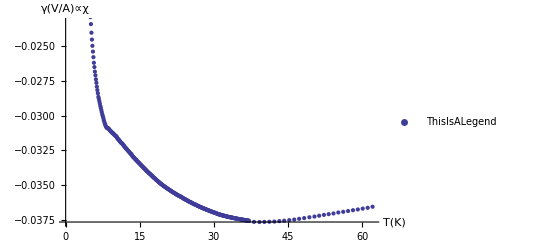

```mathematica
ListPlot[{Transpose[{T1Tot,V1Real}]},AxesLabel -> {"T(K)",Proportional["γ(V/A)",χ]},PlotLegends -> {ThisIsALegend}]
```

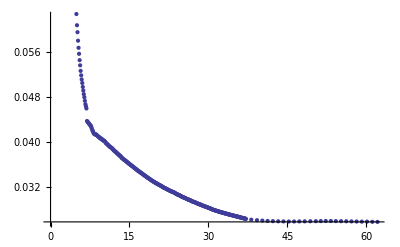

```mathematica
ListPlot[{Transpose[{T2Tot,V2Real}]},AxesLabel -> {"T(K)",Proportional["γ(V/A)",χ]},PlotLegends -> {ThisIsALegend}]
```

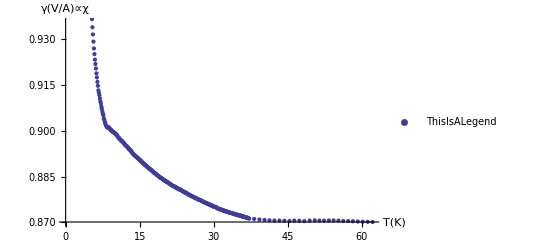

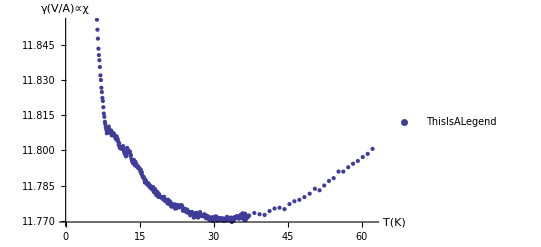

```mathematica
ListPlot[{Transpose[{T4Tot,V4Real}]},AxesLabel -> {"T(K)",Proportional["γ(V/A)",χ]},PlotLegends -> {ThisIsALegend}]
ListPlot[{Transpose[{T8Tot,V8Real}]},AxesLabel -> {"T(K)",Proportional["γ(V/A)",χ]},PlotLegends -> {ThisIsALegend}]
```

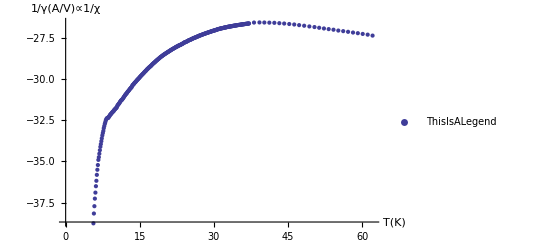

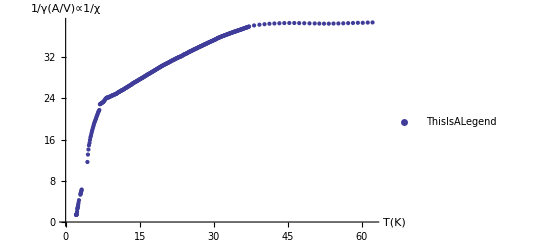

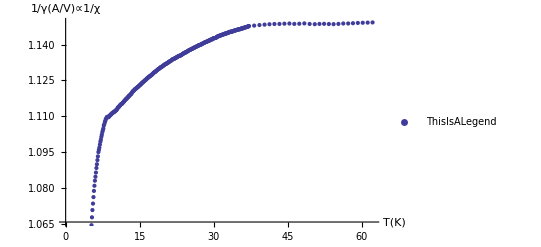

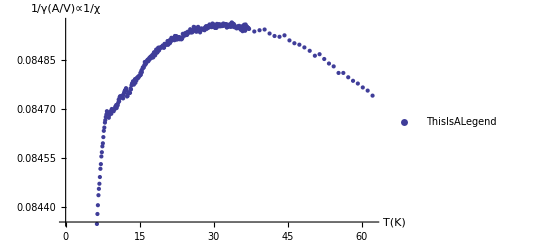

```mathematica
ListPlot[{Transpose[{T1Tot,1/V1Real}]},AxesLabel -> {"T(K)",Proportional["1/γ(A/V)",χ^-1]},PlotLegends -> {ThisIsALegend}]
ListPlot[{Transpose[{T2Tot,1/V2Real}]},AxesLabel -> {"T(K)",Proportional["1/γ(A/V)",χ^-1]},PlotLegends -> {ThisIsALegend}]
ListPlot[{Transpose[{T4Tot,1/V4Real}]},AxesLabel -> {"T(K)",Proportional["1/γ(A/V)",χ^-1]},PlotLegends -> {ThisIsALegend}]
ListPlot[{Transpose[{T8Tot,1/V8Real}]},AxesLabel -> {"T(K)",Proportional["1/γ(A/V)",χ^-1]},PlotLegends -> {ThisIsALegend}]
```

```mathematica
VOutPhase1= VMagCorr1 * Sin[θRadFull1];
VOutPhase2= VMagCorr2 * Sin[θRadFull2];
VOutPhase4= VMagCorr4* Sin[θRadFull4];
VOutPhase8= VMagCorr8* Sin[θRadFull8];
```

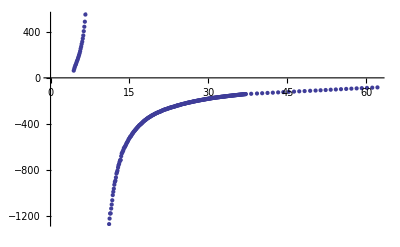

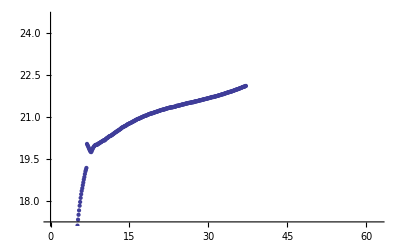

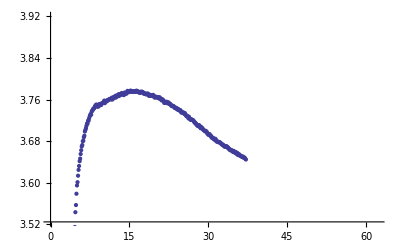

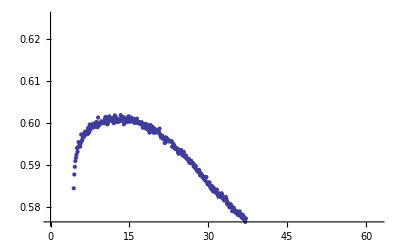

```mathematica
ListPlot[{Transpose[{T1Tot,1/VOutPhase1}]}]
ListPlot[{Transpose[{T2Tot,1/VOutPhase2}]}]
ListPlot[{Transpose[{T4Tot,1/VOutPhase4}]}]
ListPlot[{Transpose[{T8Tot,1/VOutPhase8}]}]
```